# Practical - 1

Solution of first order differential equation

Ordinary Differential Equations(ODEs), in which there is a single independent  variable and more dependent variable

1.Solve the Differential equation dy/dx=6(x^2)+2*x+3

```mathematica
sol1=DSolve[{y'[x]==6*(x^2)+2*x+3},y[x],x]
```

{{y[x]→3 x+x^2+2 x^3+C[1]}}

```mathematica
A=y[x]/.sol1/.{C[1]->1}
```

{1+3 x+x^2+2 x^3}

```mathematica
Plot[A,{x,-5,5}]
```

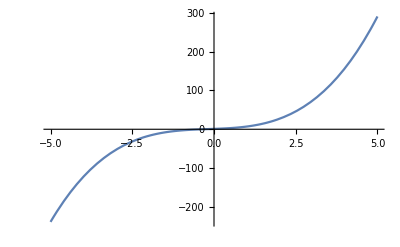

2.dy/dx=2(x^3)-x^2+x-5,y(0)=1

```mathematica
sol2=DSolve[{y'[x]==2*(x^3)-x^2+x-5,y[0]==1},y[x],x]
```

{{y[x]→1/6 (6-30 x+3 x^2-2 x^3+3 x^4)}}

```mathematica
Plot[y[x]/.sol2,{x,-2,2}]
```

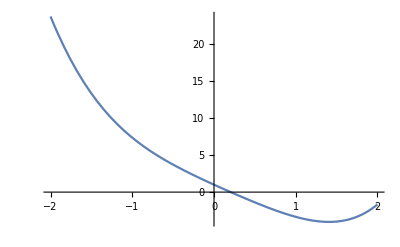

3.dy/dx+(x+2)y^2=0

```mathematica
sol3=DSolve[{y'[x]+(x+2)*y[x]^2==0},y[x],x]
```

{{y[x]→2/(4 x+x^2-2 C[1])}}

```mathematica
A=Table[y[x]/.sol3/.{C[1]->k},{k,2,5}]
```

{{2/(-4+4 x+x^2)},{2/(-6+4 x+x^2)},{2/(-8+4 x+x^2)},{2/(-10+4 x+x^2)}}

```mathematica
Plot[A,{x,-3,3}]
```

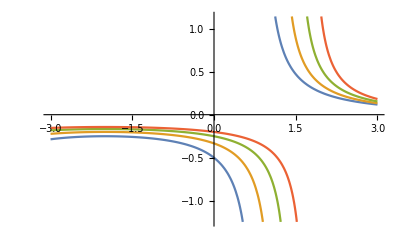

4.dy/dx=1+y^2

```mathematica
sol4=DSolve[y'[x]==1+y[x]^2,y[x],x]
```

{{y[x]→Tan[x+C[1]]}}

```mathematica
A=y[x]/.sol4/.{C[1]->1}
```

{Tan[1+x]}

```mathematica
Plot[A,{x,-4,4}]
```

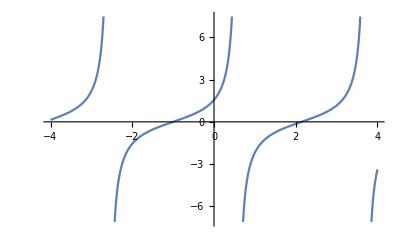

5.dy/dx=4*x+y+1

```mathematica
sol5=DSolve[y'[x]==(4*x)+y[x]+1,y[x],x]
```

{{y[x]→-5-4 x+ⅇ^x C[1]}}

```mathematica
B=y[x]/.sol5/.{C[1]->1}
```

{-5+ⅇ^x-4 x}

```mathematica
Plot[B,{x,-3,3}]
```

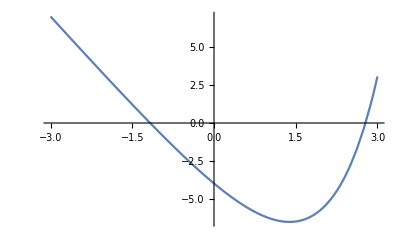

6. 2*x*y*dy/dx=x^2+y^2

```mathematica
sol6=DSolve[2*x*y[x]*y'[x]==(x^2)+y[x]^2,y[x],x]
```

{{y[x]→-√x √(x+C[1])},{y[x]→√x √(x+C[1])}}

```mathematica
B=y[x]/.sol6/.{C[1]->1}
```

{-√x √(1+x),√x √(1+x)}

```mathematica
Plot[B,{x,-3,3}]
```

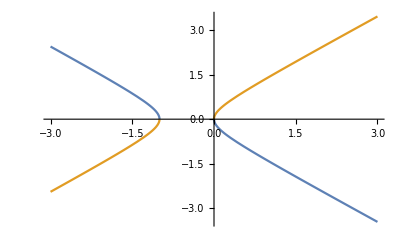

7.dy/dx=(y^2-x^2)/2*x*y

```mathematica
sol7=DSolve[y'[x]==(y[x]^2-x^2)/(2*x*y[x]),y[x],x]
```

{{y[x]→-√(-x^2+x C[1])},{y[x]→√(-x^2+x C[1])}}

```mathematica
B=y[x]/.sol7/.{C[1]->2}
```

{-√(2 x-x^2),√(2 x-x^2)}

```mathematica
Plot[B,{x,-3,3}]
```

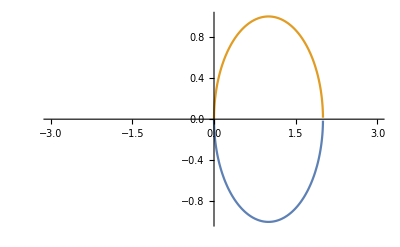

8.Check whether the following differential equations are exact or not.
a)(x+2y)dx+(2x-y)dy=0

```mathematica
P[x_,y_]:=(x+2*y)
Q[x_,y_]:=(2*x-y)
Simplify[D[P[x,y],y]-D[Q[x,y],x]]
```

0

```mathematica
eqn=(y'[x]==-P[x,y[x]]/Q[x,y[x]])
```

y'[x]==(-x-2 y[x])/(2 x-y[x])

```mathematica
Expand[eqn]
```

y'[x]==-x/(2 x-y[x])-(2 y[x])/(2 x-y[x])

```mathematica
FullSimplify[y'[x]==-x/(2 x-y[x])-(2 y[x])/(2 x-y[x])]
```

y'[x]==2+(5 x)/(-2 x+y[x])

b)(x^2+2*y^2)dx+(4*x*y-y^2)dy=0

```mathematica
P[x_,y_]:=(x^2+2*y^2)
Q[x_,y_]:=(4*x*y-y^2)
Simplify[D[P[x,y],y]-D[Q[x,y],x]]
```

0

```mathematica
eqn=(y'[x]==-P[x,y[x]]/Q[x,y[x]])
```

y'[x]==(-x^2-2 y[x]^2)/(4 x y[x]-y[x]^2)

```mathematica
Expand[eqn]
```

y'[x]==-x^2/(4 x y[x]-y[x]^2)-(2 y[x]^2)/(4 x y[x]-y[x]^2)

c)(2*x^2+2*x*y+y^2)dx+(x^2+2*x*y)dy=0

```mathematica
P[x_,y_]:=(2*x^2+2*x*y+y^2)
Q[x_,y_]:=(x^2+2*x*y)
Simplify[D[P[x,y],y]-D[Q[x,y],x]]
```

0

```mathematica
eqn=(y'[x]==-P[x,y[x]]/Q[x,y[x]])
```

y'[x]==(-2 x^2-2 x y[x]-y[x]^2)/(x^2+2 x y[x])

```mathematica
Expand[eqn]
```

y'[x]==-(2 x^2)/(x^2+2 x y[x])-(2 x y[x])/(x^2+2 x y[x])-y[x]^2/(x^2+2 x y[x])